# Goutte pendante en 3D parametrisation R(θ,ψ) (donc pas axisym) x = R sin θ cos ψ y = R sin θ sin ψ z = R cos θ

version 1

### integrator

### integrator

```mathematica
integrator[CIs_,params_,sminIN_:π,smax_:π/2,optionsin___]:=Block[
{optionsdefaut,options,optionsndsolve,

R0,p,L,ϵ,smin,
vR,R,θ,vol,aire,
equations,bcnd,equa,soluces,s,type
},


(* on traite les options *)
optionsdefaut={};options=optionsin;
If[options=="",options={}];
optionsndsolve=Sequence@@FilterRules[options,Options@NDSolve];
(* fin on traite les options *)

{R0}=CIs;
{ϵ,p}=params;

smin=sminIN;

equations={
vR'[θ]==1/R[θ]^2(-(R[θ]^2 vR[θ])/(ϵ+Tan[θ])-vR[θ]^3/(ϵ+Tan[θ])+R[θ]^3 (2-p √(R[θ]^2+vR[θ]^2)+Cos[θ] R[θ] √(R[θ]^2+vR[θ]^2))+R[θ] vR[θ]^2 (3-p √(R[θ]^2+vR[θ]^2)+Cos[θ] R[θ] √(R[θ]^2+vR[θ]^2))),
R'[θ]==vR[θ],
vol'[θ]==-2*π*R[θ]^2*Cos[θ]*Sin[θ]*(Cos[θ]*R[θ]+Sin[θ]*vR[θ])
};

bcnd={
vR[smin]==0,
R[smin]==R0,
vol[smin]==0
};

equa=Join[equations,bcnd];
(* π a π/2*)
soluces=NDSolve[
equa,{vR,R,vol},{θ,smin,smax},Method->"StiffnessSwitching"][[1]];

soluces
]
```

```mathematica
(* MaxSteps->10000,Method->"ExplicitRungeKutta" *)
```

```mathematica
"StiffnessSwitching" (* assez bien : cela passe les passages difficiles *);
```

```mathematica
(* 500 integration en 2.2 sec (home mars 2018) *)
Do[integrator[{1.1},{10^-8,0.1},π,π/2];,{500}]//Timing
```

{2.41659,Null}

```mathematica
integrator[{1.1},{10^-8,0.1},π,π/2]
```

{vR→InterpolatingFunction[{{1.5708,3.14159}},<>],R→InterpolatingFunction[{{1.5708,3.14159}},<>],vol→InterpolatingFunction[{{1.5708,3.14159}},<>]}

### Shoot

```mathematica
Shoot[grsIN_,optionsin___]:=Block[
{
optionsdefaut,options,info,Info,debug,Debug,

θL,aireL,θY,Vol,p,R0,z0,d,ϵ,
vRL,RL,volL,
vR,R,θ,vol,

s,ci,param,
smin,smax,solucesH,lstsoluces={},
valeursfinales,out,bcond
},

(* on traite les options *)
optionsdefaut={Info->0,Debug->0};options=optionsin;
If[options=="",options={}];
info=Info/.options/.optionsdefaut;
debug=Debug/.options/.optionsdefaut;
(* fin on traite les options *)

θY=grsIN[[1]];(* angle de contact *)
Vol=grsIN[[2]];(* le volume de la goutte *)
p=grsIN[[3]];
z0=grsIN[[4]];
R0=-z0;
d=grsIN[[5]];
ϵ=grsIN[[7]];

ci={R0};
param={ϵ,p};

smin=π;
smax=π/2;
solucesH=integrator[ci,param,smin,smax,options];
AppendTo[lstsoluces,solucesH];
valeursfinales={vRL,RL,volL}={vR[smax],R[smax],vol[smax]}/.solucesH;
θL=ArcCos[-vRL/Sqrt[vRL^2+RL^2]];(* on ne peut aller plus loin que π/2 de toutes les facons *)
bcond={θL-θY,volL-Vol};

out={lstsoluces,valeursfinales,bcond,θL};
(*        1            2           3     4  *)

out
]
```

### Shape

```mathematica
Shape[grsIN_,optionsin_:{}]:=Block[
{
optionsdefaut,options,info,Info,debug,Debug,zoom,Zoom,

θY,Vol,p,L,z0,
θ,R,d,

s,smin,smax,
lstfigures={},figurem,figurep,
couleurplus,couleurmoins,
out,soluces1,
RMax=0,fr

},

(* on traite les options *)
optionsdefaut={Info->0,Debug->0,Zoom->0};
options=optionsin;
If[options=="",options={}];
info=Info/.options/.optionsdefaut;
debug=Debug/.options/.optionsdefaut;
zoom=Zoom/.options/.optionsdefaut;
(* fin on traite les options *)

θY=grsIN[[1]];(* angle de contact *)
Vol=grsIN[[2]];(* le volume de la goutte *)
p=grsIN[[3]];
z0=grsIN[[4]];
d=grsIN[[5]];

couleurplus=Green;
couleurmoins=Red;

smin=π;
smax=π/2;
out=Shoot[grsIN,options];
soluces1=out[[1,1]];

RMax=Max[RMax,Abs[Table[(R[θ]/.soluces1),{θ,smin,smax,1/21.0}]]];

figurep=ParametricPlot[{R[θ]*Sin[θ],R[θ]*Cos[θ]}/.soluces1,{θ,smin,smax},AxesLabel->{"r","Z"},PlotStyle->{Thick,couleurplus},Axes->True];
figurem=ParametricPlot[{-R[θ]*Sin[θ],R[θ]*Cos[θ]}/.soluces1,{θ,smin,smax},AxesLabel->{"r","Z"},PlotStyle->{Thick,couleurmoins},Axes->True];
AppendTo[lstfigures,{figurem,figurep}];

fr=FilterRules[options,Options[Plot]];

Which[
zoom==0,out=Show[lstfigures,{fr,AxesOrigin->{0,0},PlotRange->All}],
zoom==-1,out=Show[lstfigures,{fr,AxesOrigin->{0,0},PlotRange->{{-d,d},{-RMax,RMax}}}],
zoom==-2,out=Show[lstfigures,{fr,AxesOrigin->{0,0},PlotRange->{{-1.5,1.5},{-2,0.2}}}],
True,Print["Cas non prevu : Zoom=",zoom]
];


If[info≥1,Print[out]];

out
]
```

### Info

```mathematica
Info[grsIN_]:=Block[
{out,err,couleur,bcond,Info,m3,tw,γ,wr,t},

Print["Le GRS dit : "];
Print["θY = ",grsIN[[1]]];
Print["Vol = ",grsIN[[2]]];
Print["p = ",grsIN[[3]]];
Print["z_0 = ",grsIN[[4]]];
Print["d = ",grsIN[[5]]];


Print["     -    -    -      "];

Print["Les calculs donnent : "];
out=Shoot[grsIN,{Info->1}];

bcond=out[[3]];

err=Total[Abs[bcond]];
couleur=Green;
If[err>10^-11,couleur=Blue];
If[err>10^-9,couleur=Brown];
If[err>10^-7,couleur=Red];
Print["------- ",Length[bcond],Style[" equations d'equilibre : ",couleur],Chop[bcond]];

Print["------- θL = ",out[[4]]];
Print["------- volL = ",out[[2,3]]];

]
```

### PlotSol

```mathematica
PlotSol[grsIN_,optionsin___]:=Block[
{
optionsdefaut,options,info,Info,debug,Debug,wtp,WhatToPlot,

s,smin,smax,xe,ye,ze,d1xe,d1ye,d1ze,d2xe,d2ye,d2ze,d3xe,d3ye,d3ze,
soluces1,lstsoluces,L,s1,Fγ1,ci15Ds1,out,p1,p2,fr
},

(* on traite les options *)
optionsdefaut={Info->0,Debug->0,WhatToPlot->"R[θ]"};
options=optionsin;
If[options=="",options={}];
info=Info/.options/.optionsdefaut;
debug=Debug/.options/.optionsdefaut;
wtp=WhatToPlot/.options/.optionsdefaut;
(* fin on traite les options *)


out=Shoot[grsIN,options];
lstsoluces=out[[1]];


smin=π;
smax=π/2;
soluces1=lstsoluces[[1]];
p1=Plot[ToExpression[wtp]/.soluces1,{θ,smin,smax},PlotRange->All,PlotStyle->Red];


fr=FilterRules[options,Options[Plot]];

out=Show[p1,{fr,PlotLabel->wtp,PlotRange->All}];

If[info≥1,Print[out]];

out
]
```

### routine : discretizeR

```mathematica
discretizeR[grsIN_,iθmax_,iψmax_]:=Block[
{
θY,Vol,p,R0,z0,d,ϵ,vol,

Rdis,R,θhere,R00,R1,R2,

ci,param,
θmin,θmax,solucesH,
lstout={}
},

z0=grsIN[[4]];
R0=-z0;
ci={R0};
param={grsIN[[7]],grsIN[[3]]};

θmin=π;
θmax=π/2;
solucesH=integrator[ci,param,θmin,θmax];

lstout={};

Do[
Do[

θhere=π/2+iθ/iθmax*(π-π/2);

AppendTo[lstout,Rdis[iθ,iψ]->R[θhere]/.solucesH];

,{iψ,0,iψmax}];
,{iθ,0,iθmax}];

(* --- On ajoute un point derriere π/2 *)
R00=Rdis[0,0]/.lstout;
R1=Rdis[1,0]/.lstout;
R2=Rdis[2,0]/.lstout;
Do[
AppendTo[lstout,Rdis[-1,iψ]->3*R00-3*R1+R2];
,{iψ,0,iψmax}];
(* FIN On ajoute un point derriere π/2 *)

PrependTo[lstout,{ϵ->grsIN[[7]],θY->grsIN[[1]],vol->grsIN[[2]],p->grsIN[[3]]}];


Flatten[lstout]
]
```

### Discretisation

```mathematica
deuxH=(2 R[θ,ψ]^3 Sin[θ]^3-Sin[θ] (Derivative[1,0][R][θ,ψ])^2 (Derivative[0,2][R][θ,ψ]+Cos[θ] Sin[θ] Derivative[1,0][R][θ,ψ])+3 R[θ,ψ] Sin[θ] ((Derivative[0,1][R][θ,ψ])^2+Sin[θ]^2 (Derivative[1,0][R][θ,ψ])^2)+2 Sin[θ] Derivative[0,1][R][θ,ψ] Derivative[1,0][R][θ,ψ] Derivative[1,1][R][θ,ψ]-(Derivative[0,1][R][θ,ψ])^2 (2 Cos[θ] Derivative[1,0][R][θ,ψ]+Sin[θ] Derivative[2,0][R][θ,ψ])-R[θ,ψ]^2 Sin[θ] (Derivative[0,2][R][θ,ψ]+Sin[θ] (Cos[θ] Derivative[1,0][R][θ,ψ]+Sin[θ] Derivative[2,0][R][θ,ψ])))/(R[θ,ψ] (R[θ,ψ]^2 Sin[θ]^2+(Derivative[0,1][R][θ,ψ])^2+Sin[θ]^2 (Derivative[1,0][R][θ,ψ])^2)^(3/2));
```

```mathematica
zeroPDE=deuxH-(p-R[θ,ψ]*Cos[θ]);
```

```mathematica
verif=Simplify[zeroPDE/.{D[R[θ,ψ],ψ]->0,D[R[θ,ψ],{ψ,2}]->0,R[θ,ψ]->R[θ],D[R[θ,ψ],θ]->R'[θ],D[R[θ,ψ],{θ,2}]->R''[θ]},{Sin[θ]>0}]
```

-p+Cos[θ] R[θ]+(2 R[θ]^3+3 R[θ] R'[θ]^2-Cot[θ] R'[θ]^3-R[θ]^2 (Cot[θ] R'[θ]+R''[θ]))/(R[θ] (R[θ]^2+R'[θ]^2)^(3/2))

```mathematica
zeroODE=-p+Cos[θ] R[θ]+(2 R[θ]^3+3 R[θ] R'[θ]^2-Cot[θ] R'[θ]^3-R[θ]^2 (Cot[θ] R'[θ]+R''[θ]))/(R[θ] (R[θ]^2+R'[θ]^2)^(3/2));
```

```mathematica
Simplify[verif-zeroODE/.ϵ->0,{Sin[θ]>0}]
```

0

```mathematica
(* pour le pole sud, il faut faire du travail algebrique *)
```

```mathematica
tmp1=zeroPDE/.{
D[R[θ,ψ],ψ]->0,
D[R[θ,ψ],{ψ,2}]->0
}
```

-p+Cos[θ] R[θ,ψ]+(2 R[θ,ψ]^3 Sin[θ]^3+3 R[θ,ψ] Sin[θ]^3 (R^(1,0)[θ,ψ])^2-Cos[θ] Sin[θ]^2 (R^(1,0)[θ,ψ])^3-R[θ,ψ]^2 Sin[θ]^2 (Cos[θ] R^(1,0)[θ,ψ]+Sin[θ] R^(2,0)[θ,ψ]))/(R[θ,ψ] (R[θ,ψ]^2 Sin[θ]^2+Sin[θ]^2 (R^(1,0)[θ,ψ])^2)^(3/2))

```mathematica
tmp2=Normal[Series[tmp1/.θ->π-ϵ,{ϵ,0,1}]]/.(D[R[θ,ψ],θ]/.θ->π)->0
```

-p-R[π,ψ]+(2 R[π,ψ]^4-2 R[π,ψ]^3 R^(2,0)[π,ψ])/(R[π,ψ]^2 (R[π,ψ]^2)^(3/2))+(3 ϵ R[π,ψ]^3 R^(3,0)[π,ψ])/(2 (R[π,ψ]^2)^(5/2))

```mathematica
zeroPDEenπ=Simplify[tmp2/.ϵ->0/.π->θ,{R[θ,ψ]>0}]
```

-p+2/R[θ,ψ]-R[θ,ψ]-(2 R^(2,0)[θ,ψ])/R[θ,ψ]^2

```mathematica
zeroBC=Cos[θY]+D[R[θ,ψ],θ]/Sqrt[R[θ,ψ]^2+D[R[θ,ψ],θ]^2+D[R[θ,ψ],ψ]^2]
```

Cos[θY]+(R^(1,0)[θ,ψ])/(√(R[θ,ψ]^2+(R^(0,1)[θ,ψ])^2+(R^(1,0)[θ,ψ])^2))

```mathematica
JJ=R[θ,ψ]*Sin[θ]*(Cos[θ] R[θ,ψ]+Sin[θ] Derivative[1,0][R][θ,ψ]);
ZZ=R[θ,ψ]*Cos[θ];
dvol=ZZ*JJ;
```

```mathematica
iθmax=7;
Δθ=π/2/(iθmax);
iψmax=5;
Δψ=2*π/(iψmax);
lstoutEQ={};
lstoutBC={};
volumetot=0;

Do[
Do[

θhere=π/2+iθ/iθmax*(π-π/2);
ψhere=0+iψ/iψmax*(2π-0);(* unused *)

rep={
R[θ,ψ]->Rdis[iθ,iψ],
D[R[θ,ψ],θ]->(Rdis[iθ+1,iψ]-Rdis[iθ-1,iψ])/(2*Δθ),
D[R[θ,ψ],ψ]->(Rdis[iθ,iψ+1]-Rdis[iθ,iψ-1])/(2*Δψ),
D[R[θ,ψ],{θ,2}]->(Rdis[iθ+1,iψ]-2*Rdis[iθ,iψ]+Rdis[iθ-1,iψ])/(Δθ^2),
D[R[θ,ψ],{ψ,2}]->(Rdis[iθ,iψ+1]-2*Rdis[iθ,iψ]+Rdis[iθ,iψ-1])/(Δψ^2),
D[D[R[θ,ψ],ψ],θ]->(Rdis[iθ+1,iψ+1]+Rdis[iθ-1,iψ-1]-Rdis[iθ-1,iψ+1]-Rdis[iθ+1,iψ-1])/(4*Δψ*Δθ)
};

repperiodic={
Rdis[i_,-1]->Rdis[i,iψmax-1],
Rdis[i_,iψmax+1]->Rdis[i,1]
};

repoverθ={
Rdis[iθmax+1,j_]->Rdis[iθmax-1,j]
};

If[(iθ<iθmax),
AppendTo[lstoutEQ,zeroPDE/.rep/.repoverθ/.repperiodic/.{θ->θhere}];
];

If[(iθ==iθmax),
AppendTo[lstoutEQ,zeroPDEenπ/.rep/.repoverθ/.repperiodic/.{θ->θhere}];
];


If[(iθ==0),
AppendTo[lstoutBC,zeroBC/.rep/.repperiodic/.{θ->θhere}];
];

If[(iθ<iθmax)∧(iψ<iψmax),(* une espece de methode des rectangles pour l integrale de volume *)
dvolhere=Δψ*Δθ*dvol/.rep/.{θ->θhere};
volumetot=volumetot+dvolhere;
];

,{iψ,0,iψmax}];
,{iθ,0,iθmax}];

AppendTo[lstoutBC,volumetot-vol];
```

```mathematica
(*nombre d inconnues, on met +1 car la pression est inconnue *)
(iθmax+2)*(iψmax+1)+1
```

55

```mathematica
Length[lstoutEQ]
Length[lstoutBC]
%+%%
```

48

7

55

### Test des equations discretisees sur une solution connue

```mathematica
(* un truc avec un θY = 1 radian, et plus de volume, une solution donc moins 'plate' *)
grs0={1.,3.9634264144547195,0.5610521491194301,-1.1124765586221084,1.4715572436681035,10.044677037994482,1.*^-8,8 ⅈ,9 ⅈ,10 ⅈ};
```

```mathematica
Info[grs0]
```

Le GRS dit :

θY = 1.

Vol = 3.96343

p = 0.561052

z_0 = -1.11248

d = 1.47156

-    -    -

Les calculs donnent :

------- 2 equations d'equilibre : {-2.18015×10^-9,5.49491×10^-8}

------- θL = 1.

------- volL = 3.96343

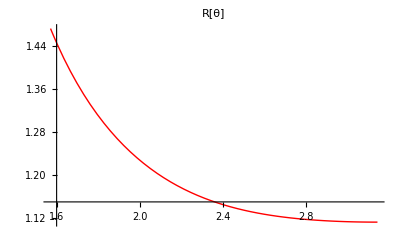

```mathematica
p1=PlotSol[grs0]
```

```mathematica
repdis=discretizeR[grs0,iθmax,iψmax]
```

{ϵ→1.×10^-8,θY→1.,vol→3.96343,p→0.561052,Rdis[0,0]→1.47156,Rdis[0,1]→1.47156,Rdis[0,2]→1.47156,Rdis[0,3]→1.47156,Rdis[0,4]→1.47156,Rdis[0,5]→1.47156,Rdis[1,0]→1.31237,Rdis[1,1]→1.31237,Rdis[1,2]→1.31237,Rdis[1,3]→1.31237,Rdis[1,4]→1.31237,Rdis[1,5]→1.31237,Rdis[2,0]→1.22105,Rdis[2,1]→1.22105,Rdis[2,2]→1.22105,Rdis[2,3]→1.22105,Rdis[2,4]→1.22105,Rdis[2,5]→1.22105,Rdis[3,0]→1.16769,Rdis[3,1]→1.16769,Rdis[3,2]→1.16769,Rdis[3,3]→1.16769,Rdis[3,4]→1.16769,Rdis[3,5]→1.16769,Rdis[4,0]→1.13755,Rdis[4,1]→1.13755,Rdis[4,2]→1.13755,Rdis[4,3]→1.13755,Rdis[4,4]→1.13755,Rdis[4,5]→1.13755,Rdis[5,0]→1.12173,Rdis[5,1]→1.12173,Rdis[5,2]→1.12173,Rdis[5,3]→1.12173,Rdis[5,4]→1.12173,Rdis[5,5]→1.12173,Rdis[6,0]→1.11451,Rdis[6,1]→1.11451,Rdis[6,2]→1.11451,Rdis[6,3]→1.11451,Rdis[6,4]→1.11451,Rdis[6,5]→1.11451,Rdis[7,0]→1.11248,Rdis[7,1]→1.11248,Rdis[7,2]→1.11248,Rdis[7,3]→1.11248,Rdis[7,4]→1.11248,Rdis[7,5]→1.11248,Rdis[-1,0]→1.69862,Rdis[-1,1]→1.69862,Rdis[-1,2]→1.69862,Rdis[-1,3]→1.69862,Rdis[-1,4]→1.69862,Rdis[-1,5]→1.69862}

```mathematica
lstoutEQ/.repdis
```

{0.361296,0.361296,0.361296,0.361296,0.361296,0.361296,-0.0211877,-0.0211877,-0.0211877,-0.0211877,-0.0211877,-0.0211877,-0.0132661,-0.0132661,-0.0132661,-0.0132661,-0.0132661,-0.0132661,-0.00981524,-0.00981524,-0.00981524,-0.00981524,-0.00981524,-0.00981524,-0.00836885,-0.00836885,-0.00836885,-0.00836885,-0.00836885,-0.00836885,-0.00849466,-0.00849466,-0.00849466,-0.00849466,-0.00849466,-0.00849466,-0.00888806,-0.00888806,-0.00888806,-0.00888806,-0.00888806,-0.00888806,-0.00608846,-0.00608846,-0.00608846,-0.00608846,-0.00608846,-0.00608846}

```mathematica
lstoutBC/.repdis
```

{0.035458,0.035458,0.035458,0.035458,0.035458,0.035458,-0.0515687}

```mathematica
vars=Table[{Rdis[iθ,iψ],Rdis[iθ,iψ]/.repdis},
{iθ,-1,iθmax,1},
{iψ,0,iψmax,1}];
vars=Flatten[vars,1];
AppendTo[vars,{p,p/.repdis}]
```

{{Rdis[-1,0],1.69862},{Rdis[-1,1],1.69862},{Rdis[-1,2],1.69862},{Rdis[-1,3],1.69862},{Rdis[-1,4],1.69862},{Rdis[-1,5],1.69862},{Rdis[0,0],1.47156},{Rdis[0,1],1.47156},{Rdis[0,2],1.47156},{Rdis[0,3],1.47156},{Rdis[0,4],1.47156},{Rdis[0,5],1.47156},{Rdis[1,0],1.31237},{Rdis[1,1],1.31237},{Rdis[1,2],1.31237},{Rdis[1,3],1.31237},{Rdis[1,4],1.31237},{Rdis[1,5],1.31237},{Rdis[2,0],1.22105},{Rdis[2,1],1.22105},{Rdis[2,2],1.22105},{Rdis[2,3],1.22105},{Rdis[2,4],1.22105},{Rdis[2,5],1.22105},{Rdis[3,0],1.16769},{Rdis[3,1],1.16769},{Rdis[3,2],1.16769},{Rdis[3,3],1.16769},{Rdis[3,4],1.16769},{Rdis[3,5],1.16769},{Rdis[4,0],1.13755},{Rdis[4,1],1.13755},{Rdis[4,2],1.13755},{Rdis[4,3],1.13755},{Rdis[4,4],1.13755},{Rdis[4,5],1.13755},{Rdis[5,0],1.12173},{Rdis[5,1],1.12173},{Rdis[5,2],1.12173},{Rdis[5,3],1.12173},{Rdis[5,4],1.12173},{Rdis[5,5],1.12173},{Rdis[6,0],1.11451},{Rdis[6,1],1.11451},{Rdis[6,2],1.11451},{Rdis[6,3],1.11451},{Rdis[6,4],1.11451},{Rdis[6,5],1.11451},{Rdis[7,0],1.11248},{Rdis[7,1],1.11248},{Rdis[7,2],1.11248},{Rdis[7,3],1.11248},{Rdis[7,4],1.11248},{Rdis[7,5],1.11248},{p,0.561052}}

```mathematica
repdisparam=Take[repdis,{1,3}]
```

{ϵ→1.×10^-8,θY→1.,vol→3.96343}

```mathematica
lstEQ=Flatten[{lstoutEQ,lstoutBC}/.repdisparam];
```

```mathematica
fr=FindRoot[lstEQ,vars,{Jacobian->{"FiniteDifference"}}]
```

{Rdis[-1,0]→1.71901,Rdis[-1,1]→1.71901,Rdis[-1,2]→1.71901,Rdis[-1,3]→1.71901,Rdis[-1,4]→1.71901,Rdis[-1,5]→1.71901,Rdis[0,0]→1.44363,Rdis[0,1]→1.44363,Rdis[0,2]→1.44363,Rdis[0,3]→1.44363,Rdis[0,4]→1.44363,Rdis[0,5]→1.44363,Rdis[1,0]→1.303,Rdis[1,1]→1.303,Rdis[1,2]→1.303,Rdis[1,3]→1.303,Rdis[1,4]→1.303,Rdis[1,5]→1.303,Rdis[2,0]→1.22516,Rdis[2,1]→1.22516,Rdis[2,2]→1.22516,Rdis[2,3]→1.22516,Rdis[2,4]→1.22516,Rdis[2,5]→1.22516,Rdis[3,0]→1.1834,Rdis[3,1]→1.1834,Rdis[3,2]→1.1834,Rdis[3,3]→1.1834,Rdis[3,4]→1.1834,Rdis[3,5]→1.1834,Rdis[4,0]→1.16346,Rdis[4,1]→1.16346,Rdis[4,2]→1.16346,Rdis[4,3]→1.16346,Rdis[4,4]→1.16346,Rdis[4,5]→1.16346,Rdis[5,0]→1.15599,Rdis[5,1]→1.15599,Rdis[5,2]→1.15599,Rdis[5,3]→1.15599,Rdis[5,4]→1.15599,Rdis[5,5]→1.15599,Rdis[6,0]→1.1543,Rdis[6,1]→1.1543,Rdis[6,2]→1.1543,Rdis[6,3]→1.1543,Rdis[6,4]→1.1543,Rdis[6,5]→1.1543,Rdis[7,0]→1.15417,Rdis[7,1]→1.15417,Rdis[7,2]→1.15417,Rdis[7,3]→1.15417,Rdis[7,4]→1.15417,Rdis[7,5]→1.15417,p→0.570863}

```mathematica
lstEQ/.fr
```

{9.99201×10^-16,8.88178×10^-16,9.99201×10^-16,-1.33227×10^-15,-1.44329×10^-15,9.99201×10^-16,-7.77156×10^-16,-1.22125×10^-15,-1.33227×10^-15,2.9976×10^-15,1.44329×10^-15,-9.99201×10^-16,1.9984×10^-15,-8.88178×10^-16,-6.66134×10^-16,-3.77476×10^-15,1.77636×10^-15,-6.66134×10^-16,-4.44089×10^-15,-1.11022×10^-15,-1.33227×10^-15,1.77636×10^-15,-1.55431×10^-15,1.55431×10^-15,3.9968×10^-15,3.33067×10^-15,3.55271×10^-15,0.,-2.22045×10^-16,-3.10862×10^-15,-4.44089×10^-16,-4.66294×10^-15,-8.88178×10^-16,-1.33227×10^-15,-1.55431×10^-15,3.77476×10^-15,-8.88178×10^-16,5.32907×10^-15,-3.10862×10^-15,4.66294×10^-15,-3.10862×10^-15,8.88178×10^-16,5.88418×10^-15,-6.88338×10^-15,5.88418×10^-15,-7.32747×10^-15,5.88418×10^-15,-6.88338×10^-15,1.11022×10^-16,0.,0.,2.22045×10^-16,1.11022×10^-16,0.,-4.44089×10^-16}

### on verifie la solution DF par rapport a la solution ODE

```mathematica
lstθ={};
lstZr={};
(* quel angle *)
iψhere=0;
Do[

θhere=π/2+iθ/iθmax*(π-π/2);
AppendTo[lstθ,{θhere,Rdis[iθ,iψhere]}/.fr];

ri=Rdis[iθ,iψhere]*Sin[θhere]/.fr;
zi=Rdis[iθ,iψhere]*Cos[θhere]/.fr;
AppendTo[lstZr,{ri,zi}]
,{iθ,0,iθmax}];
```

```mathematica
lstθ//N
```

{{1.5708,1.44363},{1.7952,1.303},{2.0196,1.22516},{2.24399,1.1834},{2.46839,1.16346},{2.69279,1.15599},{2.91719,1.1543},{3.14159,1.15417}}

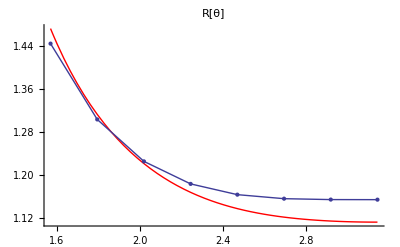

```mathematica
p2=ListPlot[lstθ,Joined->True,Mesh->All,PlotRange->All];
Show[p1,p2,PlotRange->All,AxesOrigin->{π/2,0}]
```

```mathematica
lstZr
```

{{1.44363,0},{1.27033,-0.289944},{1.10384,-0.531579},{0.925216,-0.737835},{0.725407,-0.909632},{0.501564,-1.04151},{0.256857,-1.12536},{0,-1.15417}}

```mathematica
p1Z=Shape[grs0];
```

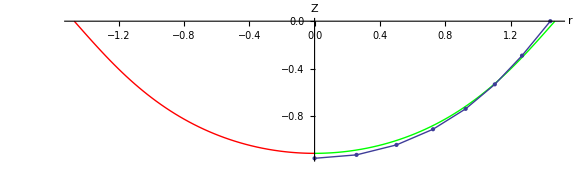

```mathematica
p2Z=ListPlot[lstZr,Joined->True,Mesh->All,PlotRange->All];
Show[p1Z,p2Z,PlotRange->All,AxesOrigin->{0,0},AspectRatio->0.3]
```